## 所得分布の生成モデル(シミュレーション)

```mathematica
(*  ver10で確認済み *)
```

```mathematica
hamada[y0_,b_,γ_,k_]:=Module[{y=y0},
Do[
If[Random[]<γ,y+=y*b,y-=y*b],{k}];
y];

hamada2[y0_,b_,γ_,k_,n_]:=Module[{data},
data=Table[hamada[y0,b,γ,k],{n}];
Histogram[data,Automatic,"Probability"]
];
```

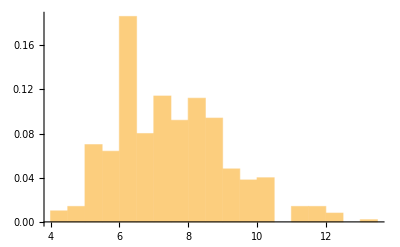

```mathematica
hamada2[10(*初期所得*),0.03(*投資割合*),0.4(*成功確率*),50(*反復時間*),500(*サンプル*)]
```

## 反復投資ゲームから予想される対数正規分布のPDF （Hamada 2004; 浜田2007）

```mathematica
logpdf[y0_,b_,γ_,k_]:=Module[{m,s,a,b2,p},
p=γ;a=Log[(1+b)/(1-b)];b2=Log[y0]+k Log[1-b];
m=b2+a k p;
s=Sqrt[k p(1-p) a^2];
Plot[PDF[LogNormalDistribution[m,s],y],{y,0,Floor[y0(1+b)^(k)]},PlotRange->{0,1}]
];
```

## 理論値 (PDF) とシミュレーションとの一致を確認する

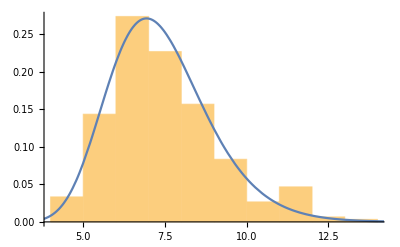

```mathematica
(* 要調整 *)
Show[hamada2[10(*初期所得*),0.03(*投資割合*),0.4(*成功確率*),50(*反復時間*),300(*サンプル*)],
logpdf[10,0.03,0.4,50]]
```

### 試作品

```mathematica
Module[{y0=10(*初期所得*),b=0.03(*投資割合*),k=250(*反復時間*),n=700(*人数*),plot1,plot2},
plot1=hamada2[y0(*初期所得*),b(*投資割合*),k(*反復時間*),n(*人数*)];
plot2=logpdf[y0(*初期所得*),b(*投資割合*),k(*反復時間*),n(*人数*)];
Show[plot1,plot2]
]
```

```mathematica
simfit[y0_,b_,k_,n_]:=Module[{plot1,plot2},
plot1=hamada2[y0(*初期所得*),b(*投資割合*),k(*反復時間*),n(*人数*)];
plot2=logpdf[y0(*初期所得*),b(*投資割合*),k(*反復時間*),n(*人数*)];
Show[plot1,plot2]
](* 関数にShowいれるとダメっぽい *)
```